```mathematica
(*Exansion of our converge rate for omega* close to 1*)
Series[4/(3-√((2-2 √(1-(1-d)^2))/(2+2 √(1-(1-d)^2))))-1,{d,0,1}]//TeXForm
```

1-\sqrt{2} \sqrt{d}+2 d+O\left(d^{3/2}\right)

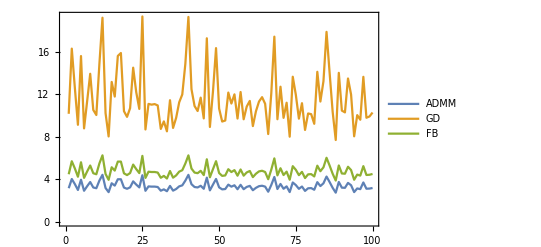

```mathematica
(*Some numerical calculations on the spectrum of different graphs*)
list={};

For[i = 1,i≤100,i=i+1,{
NumNodes = 50;
G=RandomGraph[DegreeGraphDistribution[Table[3,{NumNodes}]]];
AG=G//AdjacencyMatrix//Normal;

LG=KirchhoffMatrix[G];
SpecLG=Eigenvalues[LG+0.0];

WG=Inverse[(AG+LG)].AG;
SpecWG=Eigenvalues[WG+0.0];

lG=LineGraph[G];
AlG=lG//AdjacencyMatrix//Normal;
LlG=KirchhoffMatrix[lG];
SpecLlG=Eigenvalues[LlG+0.0];

ADMMTime =1/(√(1-RankedMax[SpecWG,2]));
GDTime =1/(1-(RankedMax[SpecLG,1]-RankedMin[SpecLG,2])/(RankedMax[SpecLG,1]+RankedMin[SpecLG,2]));
FBTime =1/(√(RankedMin[SpecLlG,2]/RankedMax[SpecLlG,1]));
AppendTo[list,{ADMMTime,GDTime,FBTime}];
}];
ListPlot[Transpose[list],Joined->True,Frame->True,PlotLegends->{"ADMM","GD","FB"}]
```

```mathematica
list//Mean
```

{3.37232,11.5693,4.76918}